```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="hT"}
theoryData=Import[StringJoin["theory-",suffix,".json"], "RawJSON"];
mcData=Import[StringJoin["mc-",suffix,".json"], "RawJSON"];
a1Data=Import[StringJoin["a1-",suffix,".json"], "RawJSON"];
a2Data=Import[StringJoin["a2-",suffix,".json"], "RawJSON"];

countErr[sample_]:=Block[{total=Total@sample,p},
Function[
p=#/total;Around[#,
3*Sqrt[total/(total-1)*(#*(1-p^2)+(total-#)*p^2)]
]
]/@sample
]
label[sample_Association,labels_]:=Block[{keys=Keys@sample,result},
result=sample;{"Mc","Alg1", "Alg2", "Theory"}
If[!MemberQ[keys,#],result[#]=0]&/@labels;
result
]
```

Suffix: hT

Energy levels: {-4.,0.,4.}

Sample sizes: 100000

<|-4.→38002,0.→59352,4.→2646|>

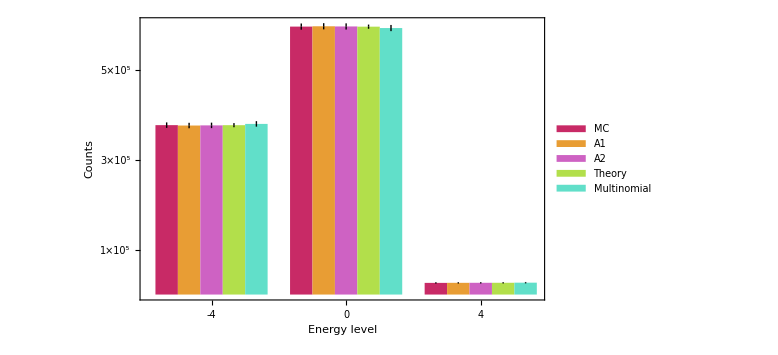

```mathematica
Row@{"Energy levels: ",labels = theoryData["energy_level"]}
{engyMc,engyA1,engyA2} =label[
Counts[#["energy_sample"]],labels
]&/@{mcData,a1Data,a2Data};

Row@{"Sample sizes: ",sampleSize=Total@Values@engyMc}
Assert@And[
sampleSize==Total[Values@engyA1],
sampleSize==Total[Values@engyA2]
]

(* Theory and example of a multinomial sample *)
drb=MultinomialDistribution[sampleSize, theoryData["energy_probs"]];
engyTheory =Association@MapThread[
Rule[#1,#2]&,{labels,sampleSize*theoryData["energy_probs"]}
];
err=3*StandardDeviation@drb;
SeedRandom@0;engyExample=Association@MapThread[
Rule[#1,#2]&,{labels,RandomVariate@drb}
]

(* Adding errors *)
{engyMc,engyA1,engyA2,engyExample}=countErr/@{
engyMc,engyA1,engyA2,engyExample
};
engyTheory=Association@MapThread[
Rule[#1,Around[#2,#3]]&,{Keys@engyTheory,Values@engyTheory,err}
];

(* Rearranging bars *)
bars=Transpose[Values/@{KeySort[engyMc],KeySort[engyA1],KeySort[engyA2],engyTheory,engyExample}];
colors = Table[ColorData[54][i],{i,6}];
baseStyle = Directive[Black, FontFamily->"Arial", FontSize->16];
frameStyle = Append[baseStyle, Thickness@0.003];

BarChart[
bars,ChartStyle->(Directive[EdgeForm@None,FaceForm@#]&/@colors),

FrameLabel->{
{"Counts",None},{"Energy level",None}
},
FrameTicks->{
{Table[
{i*10^4,Row@{i,"×",Superscript[10,5]}},
{i,1,10,2}
],None},
{Join[
Table[{6*i+0.5,Null,{0,0.02}},{i,5}],
Table[{6*i-2.5,Round@labels[[i]],{0,0}},{i,Length@bars}]
],None}
},
FrameTicksStyle->Thickness@0.003,

ChartLayout->"Grouped",BarSpacing->{0,1},
Epilog->{
Inset[SwatchLegend[
Directive[EdgeForm@None,FaceForm@#]&/@colors,
{"MC","A1","A2","Theory","Multinomial"}
],Scaled@{0.75,0.75}]
},

BaseStyle->baseStyle,
Axes->False,Frame->True,FrameStyle->Thickness@0.003,
ImageSize->Large
]
```